1+10 (1-ⅇ^(-t/10))

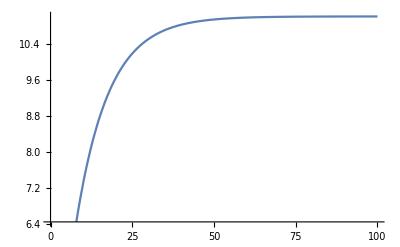

1+10 ⅇ^(-t/10)

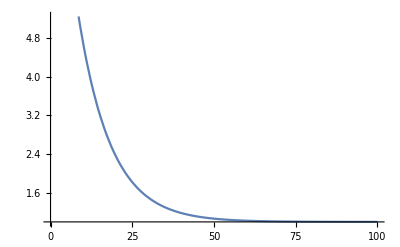

```mathematica
Clear["Global`*"]
R = 10;
Is = 1;
Cs=1;
τ=R*Cs;
urest=1;
(*输入电流脉冲*)
u=urest+R*Is*(1-E^(-t/τ))
Plot[u,{t,0,100}]
(*无电流输入*)
u=urest+R*Is*E^(-t/τ)
Plot[u,{t,0,100}]
```